## Define parameter values (instead of importing)

```mathematica
ClearMech[];ClearAll["Global`*"]; Needs["MechanicalSystems`Modeler2D`"];Off[General::"spell"];Off[General::"spelll"];
```

ClearAll::wrsym: Symbol T is Protected.

Linkage lengths (SI units)

```mathematica
L1In=5.26 *10^-3;
L2In=2.2 *10^-3;
L3In=.81*10^-3;
L4In=4.8 *10^-3;
EXLocalIn = 1.43 *10^-3 ;
EYLocalIn = 1.64 *10^-3 ;
FXLocalIn = 5.52 *10^-3 ;
FYLocalIn = 4.3 *10^-3;
```

Dactyl/propdus mass

```mathematica
dMassIn = 4.53 *10^-4;
```

Dactyl/propdus moment of inertia

```mathematica
dIIn= 8.16 *10^-8 ; (* (kg m^2) *)
waterIIn = 1*10^-8;(* (kg m^2) *)
```

Spring at the mV joint (linear spring stiffness (N/m) * L2^2 (approx. distance to force application)

```mathematica
kSpringIn =0.1 (60*10^3) (3.18 *10^-3)^2;    (* Torsion spring stiffness (Nm/rad) *)
```

Max torque estimated as max force (29 N in Zack et al paper), times L2 (3.18e-3, approximate distance to force application)

```mathematica
thetaRestIn =  ((90-70)/180) N[π];
```

Duration of simulation (s)

```mathematica
simDurationIn = 8*10^-3;
```

Initial input angle, θin, at the mV joint

```mathematica
thetaStartIn = ((90-35)/180) N[π];
```

```mathematica
dAIn=1.5 * 10^-11;
rhoIn=998;
CdIn = 0*1;
```

Check that the geometry is possible (both should be 'True')

```mathematica
mxErrIn = 10^-5;
```

## Import parameter values (instead of defining)

### Set parameters

```mathematica
KillMech[];ClearMech[];ClearAll["Global`*"]; Needs["MechanicalSystems`Modeler2D`"];Off[General::"spell"];
```

ClearMech::shdw: Symbol "ClearMech" appears in multiple contexts {"MechanicalSystems`Modeler2D`", "Global`"}; definitions in context "MechanicalSystems`Modeler2D`" may shadow or be shadowed by other definitions.

```mathematica
currPath = Import["/Volumes/Docs/Projects/Patek_project/pod_model/sims/curr_path.txt",{"Text","Lines"}];
```

```mathematica
currPath
```

{/Volumes/Docs/Projects/Patek_project/pod_model/sims/s001}

```mathematica
inParams = Import[StringJoin[currPath, "/input_params.mat"]][[1]];
```

```mathematica
tEvalIn = Import[StringJoin[currPath, "/eval_time.mat"]][[1]];
```

```mathematica
L1In = inParams[[1]];
L2In=inParams[[2]];
L3In=inParams[[3]];
L4In=inParams[[4]];

EXLocalIn = inParams[[5]];
EYLocalIn=inParams[[6]];
FXLocalIn=inParams[[7]];
FYLocalIn=inParams[[8]];

thetaStartIn=inParams[[9]];
dMassIn=inParams[[10]];
dIIn=inParams[[11]];
kSpringIn=inParams[[12]];
thetaRestIn=inParams[[13]];

simDurationIn=inParams[[14]];
dAIn=inParams[[15]];
rhoIn=inParams[[16]];
CdIn=inParams[[17]];
waterIIn = inParams[[18]];
mxErrIn = inParams[[19]];
```

```mathematica
Clear[inParams]
```

## Linkage model

### Rescale input parameter values

Scale Factors (Mutliplers of all parameters -- helps with numerical instabilities)

```mathematica
sL = 1 / L1In;
sM = 1/dMassIn;
sT=10^3;
```

```mathematica
(* Apply scale factors to parameters *)
dMass = dMassIn sM;
dI= dIIn sM sL^2;
waterI=waterIIn sM sL^2;

L1=L1In sL;
L2=L2In sL;
L3=L3In sL;
L4=L4In  sL;

EXLocal = EXLocalIn sL;
EYLocal = EYLocalIn sL;
FXLocal = FXLocalIn sL;
FYLocal = FYLocalIn sL;
thetaStart    = thetaStartIn;

kSpring = kSpringIn (sM sL^2/sT^2);
thetaRest= thetaRestIn;
dA = dAIn * sL^5;
rho = rhoIn * sM / sL^3;
Cd = CdIn;

simDuration = simDurationIn * sT;
tEval = tEvalIn*sT;

mxErr = mxErrIn;
```

```mathematica
Clear[dMassIn, dIIn,L1In,L2In,L3In,L4In,kSpringIn,TmaxIn,EXLocalIn,EYLocalIn,FXLocalIn,FYLocalIn,thetaIn,simDurationIn,tEvalIn,simDurationIn,tEvalIn,dAIn,rhoIn,CdIn,waterIIn,mxErrIn]
```

### Calculated parameter values, define model inputs

Angle, ψ, btwn L1 & L4:

```mathematica
(* This angle ?*)
si[theta_]:=ArcCos[(h[theta]^2+L1^2-L2^2)/(2 h[theta] L1)]+ArcCos[(h[theta]^2+L4^2-L3^2)/(2 h[theta] L4)];
(* Distance btwn D & B: *)
h[theta_]:=√(L1^2+L2^2-2 L1 L2 Cos[theta]);
```

Check that the geometry is possible (both should be 'True')

```mathematica
L4  < ( L3 + h[thetaStart])
```

True

```mathematica
h[thetaStart]
```

0.833748

```mathematica
L3
```

0.153992

```mathematica
L4
```

0.912548

```mathematica
L4  > (  h[thetaStart]-L3)
```

True

```mathematica
thetaStart
```

0.959931

Points on the appendage

```mathematica
AX=0;
AY= 0;
BX=L2 Sin[thetaStart];
BY=L2 Cos[thetaStart];
CX=L4 Sin[si[thetaStart]];
CY=L1-L4 Cos[si[thetaStart]];
DX=0;
DY=L1;
EX =BX+ EXLocal;
EY=BY - EYLocal;
FX=BX- FXLocal;
FY=EY-FYLocal;
```

```mathematica
Clear[si,h]
```

Body addresses

```mathematica
ground = 1; mV = 2;carpus = 3;dactyl = 4;
```

Display initial geometry

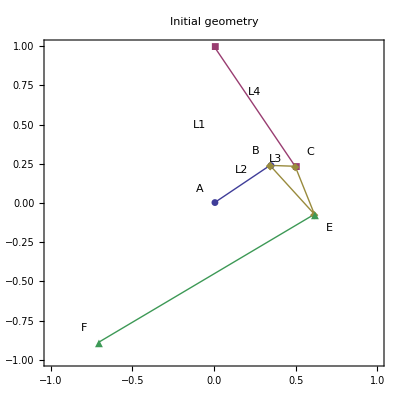

```mathematica
offset = .09 L1;
Show[
ListPlot[{
{{AX,AY},{BX,BY}},
{{CX,CY},{DX,DY}},
{{BX,BY},{EX,EY},{CX,CY},{BX,BY}},
{{EX,EY},{FX,FY}}
},
PlotMarkers->Automatic,Joined->True,
Frame->True,AspectRatio->Automatic,
PlotLabel->"Initial geometry",
PlotRange->{{-1,1},{-1,1}}],
Graphics[
{Text["A",{AX-offset,AY+offset}],Text["B",{BX-offset,BY+offset}],
Text["C",{CX+offset,CY+offset}],Text["D",{DX-offset,DY+offset}],
Text["E",{EX+offset,EY-offset}],Text["F",{FX-offset,FY+offset}],
Text["L1",{Mean[{AX,DX}]-offset,Mean[{AY,DY}]}],
Text["L2",{Mean[{AX,BX}]-offset,Mean[{AY,BY}]}+offset],
Text["L3",{Mean[{CX,BX}]-offset,Mean[{CY,BY}]}+offset/2],
Text["L4",{Mean[{DX,CX}]-offset,Mean[{DY,CY}]}+offset]
}]
]
```

### Define Bodies

```mathematica
bd[ground] = Body[ground,
PointList->{
(*P1*){DX,DY}},
InitialGuess->{
{0,0},0}
];
```

```mathematica
bd[mV] = Body[mV,
PointList->{
(*P1*){BX,BY}},
Centroid->{0,0},
InitialGuess->{
{0,0},0}
];
```

```mathematica
bd[carpus] = Body[carpus,
   PointList -> {
     (*P1*){ CX - BX, CY - BY},
     (*P2*){ EX - BX, EY - BY}},
Centroid->{0,0},
         InitialGuess -> {
               {BX, BY}, 0}
         ];
```

```mathematica
bd[dactyl] = Body[dactyl,
      PointList -> {
          (*P1*){FX - EX, FX - EX}},
Mass ->dMass,
Inertia ->dI+waterI,
Centroid->{0,0},
      InitialGuess -> {
         {EX, EY}, 0}
      ];
```

```mathematica
SetBodies[bd[ground],bd[mV],bd[carpus],bd[dactyl]];
```

### Define constraints

Pin joint between ground and mV:

```mathematica
cs[1]= Revolute2[1,Point[ground,0],Point[mV,0]];
```

Initially fix position of joint at mV origin (removed later):

```mathematica
cs[2] = RotationLock1[2,  mV,0];
```

Pin joint between carpus and mV:

```mathematica
cs[3] = Revolute2[3, Point[carpus, 0], Point[mV, 1]];
```

Fix distance between ground and top of carpus:

```mathematica
cs[4] = RelativeDistance1[4, Point[carpus, 1], Point[ground, 1], L4];
```

Pin btwn carpus and dactyl

```mathematica
cs[5] = Revolute2[5, Point[dactyl, 0], Point[carpus, 2]];
```

Lock rotation btwn carpus & dactyl

```mathematica
cs[6] = RotationLock1[6, carpus, dactyl, 0];
```

```mathematica
SetConstraints[cs[1], cs[2], cs[3], cs[4],cs[5],cs[6]];
```

```mathematica
Print["Check system after constraints:" Evaluate[CheckSystem[]]]
```

Check system after constraints: True

### Evaluate kinematic model

SetParameters[{
   (*Torsion spring stiffness*)  theta -> θ
   }];

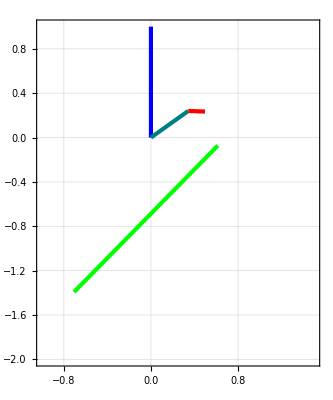

```mathematica
graph=Graphics[{
(*ground*){RGBColor[0,0,1],Bar[Axis[ground,0,1],10^-4 sL,10^-4 sL]},
(*mV*){RGBColor[0,.5,.5],Bar[Line[mV,0,1],10^-4 sL,10^-4 sL]},
(*carpus*){RGBColor[1,0,0],Bar[Line[carpus,0,1],10^-4 sL,10^-4 sL]},
(*dactyl*){RGBColor[0,1,0],Bar[Line[dactyl,0,1],10^-4 sL,10^-4 sL]}
},
Frame->True,
AspectRatio->Automatic,
GridLines->Automatic,
PlotRange->{{-1,1.5},{-2,1}}
];

Show[graph/.SolveMech[]]
```

```mathematica
Evaluate[{Angle[mV,1]}/.SolveMech[]] (180/π)
```

{35.}

### Define Loads

Moment created by the spring

```mathematica
springMoment=-kSpring  ( Angle[mV,1]-thetaRest);
dragMoment=(-0.5*rho*Cd*(Velocity[dactyl][[3]])^2*dA) (Velocity[dactyl][[3]]/Abs[10^-20+Velocity[dactyl][[3]]]);
```

```mathematica
ld[1]=Moment[mV,springMoment];
```

Drag on dactyl

ld[2] = Force[dactyl, Axis[Point[dactyl, 1], -Velocity[dactyl, 1]^2], 5.0, Magnitude -> Relative];

```mathematica
ld[2]=Moment[dactyl,0*dragMoment];
```

TODO: Add Acceleration reaction on dactyl

```mathematica
ld[3]=Gravity[{0,-1},0];
```

```mathematica
SetLoads[ld[1],ld[2]]
```

```mathematica
Print["Check system after loads:" Evaluate[CheckSystem[]]]
```

Check system after loads: True

### Find solution

Solution with the 4-bar linkage constrained from moving:

Remove constraint 2 (fixed angle of the mV)  & define initial conditions

```mathematica
fsys = SetFree[2,{Solution->Dynamic,
InitialCondition->{T->0,Θ2d->0,Θ3d->0,Θ4d->0,X2d->0,Y2d->0,X3d->0,Y3d->0,X4d->0,Y4d->0}}];
```

SolveFree[fsys]

```mathematica
(* Default solver *)
sol = SolveFree[fsys, simDuration, MakeRules -> {Location, Velocity, Acceleration},
MaxError->mxErr];
```

(* High precision solver *)
sol = SolveFree[fsys, simDuration, MakeRules -> {Location, Velocity, Acceleration},
   ConstraintCorrection -> True,
   MaxError -> 10^-7,
   Method -> Corrector,
   FitDegree -> Quadratic,
   MaxSteps -> 5000];

### Simulation diagnostics (for debugging)

```mathematica
Constraints[1]/.sol
Constraints[3]/.sol
Constraints[4]/.sol
```

{0,0}

{-0.342611 Cos[InterpolatingFunction[{{0.,8.}},<>][T]]+0.239899 Sin[InterpolatingFunction[{{0.,8.}},<>][T]]+InterpolatingFunction[{{0.,8.}},<>][T],-0.239899 Cos[InterpolatingFunction[{{0.,8.}},<>][T]]-0.342611 Sin[InterpolatingFunction[{{0.,8.}},<>][T]]+InterpolatingFunction[{{0.,8.}},<>][T]}

{-0.832743+(-1.-0.00555379 Cos[InterpolatingFunction[{{0.,8.}},<>][T]]+0.153892 Sin[InterpolatingFunction[{{0.,8.}},<>][T]]+InterpolatingFunction[{{0.,8.}},<>][T])^2+(0.153892 Cos[InterpolatingFunction[{{0.,8.}},<>][T]]+0.00555379 Sin[InterpolatingFunction[{{0.,8.}},<>][T]]+InterpolatingFunction[{{0.,8.}},<>][T])^2}

```mathematica
StepMech[]
```

{X2→0.,Y2→0.,Θ2→0.,X3→0.342611,Y3→0.239899,Θ3→0.,X4→0.614474,Y4→-0.0718882,Θ4→0.}

```mathematica
Loads[dactyl,Coordinates->Global][[2]]
```

0

```mathematica
(Loads[carpus,Coordinates->Global])/.sol/.{T->tEval}
```

{{0,0},0}

### Draw bodies

```mathematica
graph = Graphics[{
{RGBColor[0, 0, 1], Bar[Line[ground, 0, 1], sL/10^4, sL/10^4]}, 
{RGBColor[0, 0.5, 0.5], Bar[Line[mV, 0, 1], sL/10^4, sL/10^4]}, 
{RGBColor[1, 0, 0], Bar[Line[carpus, 0, 1], sL/10^4, sL/10^4]}, 
{RGBColor[0, 1, 0], Bar[Line[dactyl, 0, 1], sL/10^4, sL/10^4]}}, 
Frame -> True, AspectRatio -> Automatic, GridLines -> Automatic];
```

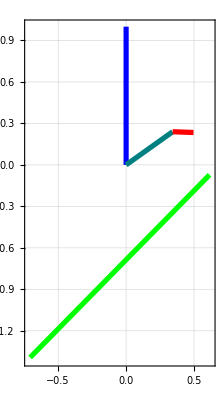

```mathematica
Show[graph/.(sol/.{T->0*simDuration})]
```

numPlot = 10; GraphicsGrid[{graph /. (sol /. Table[{T -> i}, {i, 0, simDuration, simDuration/numPlot}] )}]

```mathematica
Animate[Show[graph /. (sol /. {T -> i})], {i, 0, simDuration, .1}]
```

### Graph results

Theta (angle btwn mV and ground (L1))

```mathematica
(180/Pi) Angle[mV,1]/.sol/.{T->0}
```

35.

```mathematica
thetaStart (180/Pi)
```

55.

```mathematica
thetaRest
```

0.349066

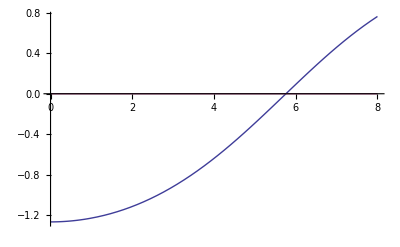

```mathematica
Plot[{(springMoment/.sol),T*0},{T,0,simDuration}]
```

```mathematica
(180/Pi) Tmax/kSpring
```

11.8355 Tmax

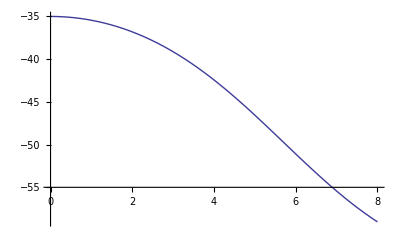

```mathematica
(* Moment on mV *)
Plot[(180/Pi)((Angle[mV,1])-(Pi/2-thetaRest))/.sol,{T,0,simDuration}]
```

```mathematica
(180/Pi)thetaRest
```

20.

```mathematica
springMoment/.sol/.{T->0}
```

-1.26737

```mathematica
(Pi/2-Angle[mV,1]-thetaRest)kSpring/.sol/.{T->0}
```

2.9572

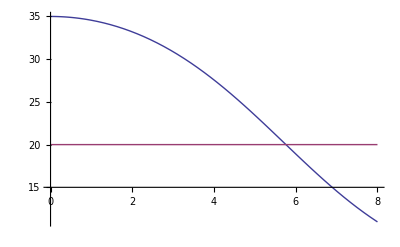

```mathematica
(* Moment on mV *)
Plot[{(180/Pi)(Angle[mV,1])/.sol,0 T+(180/Pi) thetaRest},{T,0,simDuration}]
```

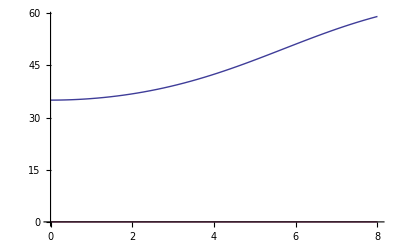

```mathematica
(* Moment on mV *)
Plot[{(180/Pi)(Pi/2-Angle[mV,1]-thetaRest)/.sol,0 T},{T,0,simDuration}]
```

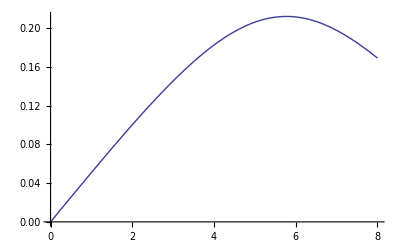

```mathematica
Plot[Velocity[dactyl][[3]]/.sol,{T,0,simDuration}]
```

### Energetics

springEnergy[T_] := -((Angle[mV, 1] - thetaRest)/Abs[(Angle[mV, 1] - thetaRest)]) 0.5 kSpring (Angle[mV, 1] - thetaRest)^2 ;

```mathematica
springEnergy=Abs[0.5springMoment(Angle[mV,1]-thetaRest)/.sol];
```

```mathematica
dacSpeed=Sqrt[
(Velocity[carpus,2][[1]])^2+(Velocity[carpus,2][[2]])^2]/.sol;
```

dragEnergy[ti_] := NIntegrate[totDrag[t], {t, 0, ti}];

```mathematica
kineEnergy=(*Rotation *)(0.5 (dI+waterI) Velocity[dactyl][[3]]^2  +
        (* Translation *) 0.5 dMass dacSpeed^2)/.sol;
```

```mathematica
totEnergy = springEnergy  + kineEnergy;
```

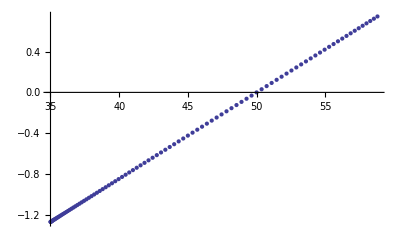

```mathematica
ListPlot[Table[{((180/Pi) (Pi/2-Angle[mV,1] -thetaRest)) /. sol, springMoment /. sol}, {T, simDuration/100, simDuration - simDuration/100, simDuration/100}]]
```

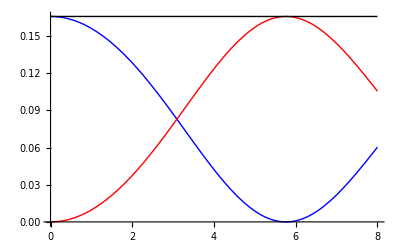

```mathematica
kinePlot=Plot[kineEnergy,{T,0,simDuration},DisplayFunction->Identity,PlotStyle->RGBColor[1, 0,0]];
springPlot=Plot[springEnergy,{T,0,simDuration},DisplayFunction->Identity,PlotStyle->{RGBColor[0, 0,1]}];
totPlot=Plot[totEnergy,{T,0,simDuration},DisplayFunction->Identity,PlotStyle->{RGBColor[0, 0,0]}];

Show[springPlot,kinePlot,totPlot,DisplayFunction->$DisplayFunction]
```

```mathematica
kinePlot=Plot[kineEnergy[All]/.sol,{T,0,simDuration},DisplayFunction->Identity,PlotStyle->RGBColor[1, 0,0]];
springPlot=Plot[springEnergy[T]/.sol,{T,0,simDuration},DisplayFunction->Identity,PlotStyle->{RGBColor[0, 0,1],Dashed}];
totPlot=Plot[(kineEnergy[T]+springEnergy[T])/.sol,{T,0,simDuration},DisplayFunction->Identity,PlotStyle->{RGBColor[0, 0,0]}];
Show[springPlot,kinePlot,totPlot,DisplayFunction->$DisplayFunction]
```

-Graphics-

```mathematica
springEnergy[T]/.sol/.{T->3}
```

0.087138[3]

### Export data

```mathematica
(* P1 on carpus *)
carp1Kine=
{((Location[Point[carpus,1]]/.sol/.{T->tEval})/sL)[[1]],((Location[Point[carpus,1]]/.sol/.{T->tEval})/sL)[[2]],
((Velocity[Point[carpus,1]]/.sol/.{T->tEval})/sL * sT)[[1]],((Velocity[Point[carpus,1]]/.sol/.{T->tEval})/sL * sT)[[2]],
((Acceleration[Point[carpus,1]]/.sol/.{T->tEval})/sL * sT^2)[[1]],((Acceleration[Point[carpus,1]]/.sol/.{T->tEval})/sL * sT^2)[[2]]
};
Export[StringJoin[currPath, "/carpusP1.mat"],carp1Kine,"MAT"];
```

StringJoin::string: String expected at position 1 in currPath <> "/carpusP1.mat".

Export::chtype: First argument currPath <> "/carpusP1.mat" is not a valid file specification.

```mathematica
(* P2 on carpus *)
carp2Kine=
{((Location[Point[carpus,2]]/.sol/.{T->tEval})/sL)[[1]],((Location[Point[carpus,2]]/.sol/.{T->tEval})/sL)[[2]],
((Velocity[Point[carpus,2]]/.sol/.{T->tEval})/sL * sT)[[1]],((Velocity[Point[carpus,2]]/.sol/.{T->tEval})/sL * sT)[[2]],
((Acceleration[Point[carpus,2]]/.sol/.{T->tEval})/sL * sT^2)[[1]],((Acceleration[Point[carpus,2]]/.sol/.{T->tEval})/sL * sT^2)[[2]]
};
Export[StringJoin[currPath, "/carpusP2.mat"],carp2Kine,"MAT"];
```

StringJoin::string: String expected at position 1 in currPath <> "/carpusP2.mat".

Export::chtype: First argument currPath <> "/carpusP2.mat" is not a valid file specification.

```mathematica
(* P1 on ground *)
gnd1Kine=
{((Location[Point[ground,1]]/.sol/.{T->tEval})/sL)[[1]],((Location[Point[ground,1]]/.sol/.{T->tEval})/sL)[[2]],
((Velocity[Point[ground,1]]/.sol/.{T->tEval})/sL * sT)[[1]],((Velocity[Point[ground,1]]/.sol/.{T->tEval})/sL * sT)[[2]],
((Acceleration[Point[ground,1]]/.sol/.{T->tEval})/sL * sT^2)[[1]],((Acceleration[Point[ground,1]]/.sol/.{T->tEval})/sL * sT^2)[[2]]
};
Export[StringJoin[currPath, "/groundP1.mat"],gnd1Kine,"MAT"];
```

StringJoin::string: String expected at position 1 in currPath <> "/groundP1.mat".

Export::chtype: First argument currPath <> "/groundP1.mat" is not a valid file specification.

```mathematica
(* P1 on mV *)
mV1Kine=
{((Location[Point[mV,1]]/.sol/.{T->tEval})/sL)[[1]],((Location[Point[mV,1]]/.sol/.{T->tEval})/sL)[[2]],
((Velocity[Point[mV,1]]/.sol/.{T->tEval})/sL * sT)[[1]],((Velocity[Point[mV,1]]/.sol/.{T->tEval})/sL * sT)[[2]],
((Acceleration[Point[mV,1]]/.sol/.{T->tEval})/sL * sT^2)[[1]],((Acceleration[Point[mV,1]]/.sol/.{T->tEval})/sL * sT^2)[[2]]
};
Export[StringJoin[currPath, "/mVP1.mat"],mV1Kine,"MAT"];
```

StringJoin::string: String expected at position 1 in currPath <> "/mVP1.mat".

Export::chtype: First argument currPath <> "/mVP1.mat" is not a valid file specification.

```mathematica
(* P1 on dactyl *)
dac1Kine=
{((Location[Point[dactyl,1]]/.sol/.{T->tEval})/sL)[[1]],((Location[Point[dactyl,1]]/.sol/.{T->tEval})/sL)[[2]],
((Velocity[Point[dactyl,1]]/.sol/.{T->tEval})/sL * sT)[[1]],((Velocity[Point[dactyl,1]]/.sol/.{T->tEval})/sL * sT)[[2]],
((Acceleration[Point[dactyl,1]]/.sol/.{T->tEval})/sL * sT^2)[[1]],((Acceleration[Point[dactyl,1]]/.sol/.{T->tEval})/sL * sT^2)[[2]]
};
Export[StringJoin[currPath, "/dactylP1.mat"],dac1Kine,"MAT"];
```

StringJoin::string: String expected at position 1 in currPath <> "/dactylP1.mat".

Export::chtype: First argument currPath <> "/dactylP1.mat" is not a valid file specification.

```mathematica
(* Moment from spring *)
springM = (springMoment
/.sol/.{T->tEval})/sM/sL^2*sT^2;
Export[StringJoin[currPath, "/springMoment.mat"],springM,"MAT"];
```

StringJoin::string: String expected at position 1 in currPath <> "/springMoment.mat".

Export::chtype: First argument currPath <> "/springMoment.mat" is not a valid file specification.

```mathematica
(* Moment from drag *)
dragM = (dragMoment
/.sol/.{T->tEval}) /sM/sL^2*sT^2;
Export[StringJoin[currPath, "/dragMoment.mat"],dragM,"MAT"];
```

StringJoin::string: String expected at position 1 in currPath <> "/dragMoment.mat".

Export::chtype: First argument currPath <> "/dragMoment.mat" is not a valid file specification.